## Parameters

```mathematica
sampleSizeArray={10000,10000,10000,10000,10000};
nArray={15,15,25,25,30};
alphaArray={2,2,2,2,2};
thetaArray={0.1,0.5,3,6,10};
muArray={1,1,1,1,1};
(*colorArray=RandomColor[length];*)
colorArray={Orange,Red,Blue,Brown,Black};
rootDir="D:\\research\\eigenvectors\\simulations\\data\\asymptotic";

simulatedDataFile="simulation_5.mx";
analyticalDataFile="analytical_min_cdf_5.mx";


If[
Min[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray],Length[muArray]}]<Max[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray],Length[muArray]}],Print["Missing parameters!!"];length=0;,
length=Min[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}];
];
simulatedDataFile=FileNameJoin[{rootDir,simulatedDataFile}];
analyticalDataFile=FileNameJoin[{rootDir,analyticalDataFile}];
```

## Samples generation

```mathematica
Print["Time taken to generate samples: ",AbsoluteTiming[simDataArray=Table[
n=nArray[[t]];
alpha=alphaArray[[t]];
theta=thetaArray[[t]];
sampleSize=sampleSizeArray[[t]];

m=n+alpha;
u=Table[x,{x,Normalize[RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]],n].{1.,0}]}];
sigma = FullSimplify[IdentityMatrix[n]+theta*Outer[Times,u,Conjugate[u]]];

ParallelTable[
A=Table[Flatten[RandomReal[MultinormalDistribution[Table[0,n],sigma/2],1]+I*RandomReal[MultinormalDistribution[Table[0,n],sigma/2],1]],m];
W=ConjugateTranspose[A].A; 
eigSys=Eigensystem[W];
{eigSys[[1]],eigSys[[2]],u}
,sampleSize],
{t,1,length}];][[1]]," seconds"];
AppendTo[simDataArray,{sampleSizeArray,nArray,alphaArray,thetaArray,muArray}];
Print["Exported to: ",Export[simulatedDataFile,simDataArray]];
```

Time taken to generate samples: 782.152 seconds

Exported to: D:\research\eigenvectors\simulations\data\asymptotic\simulation_5.mx

## Analytical expression

```mathematica
Clear[pdf];



(*generic pdf min eigvec asymptotic behaviour*)
(*
anaMin=0; anaMax=5;dv=0.005;
description="generic pdf min eigvec asymptotic behaviour";
pdf[v_,alpha_,mu_,theta_,beta_]:=mu/(1-beta)*Exp[-(mu*v)/(1-beta)];
*)




(*generic cdf min eigvec asymptotic behaviour*)
anaMin=0; anaMax=5;dv=0.005;
description="generic pdf min eigvec asymptotic behaviour";
pdf[v_,alpha_,mu_,theta_,beta_]:=1-Exp[-(mu*v)/(1-beta)];





anaDataArray=Table[
alpha=alphaArray[[t]];
theta=thetaArray[[t]];
mu=muArray[[t]];
beta=theta/(theta+1);
{v,pdf[v,alpha,mu,theta,beta]},{v,anaMin,anaMax,dv}
,{t,1,length}];
AppendTo[anaDataArray,{description,alphaArray,thetaArray,muArray}];
Print["Exported to: ",Export[analyticalDataFile,anaDataArray]];
```

Exported to: D:\research\eigenvectors\simulations\data\asymptotic\analytical_min_cdf_5.mx

## Import data

```mathematica
simDataArray=Import[simulatedDataFile];
anaDataArray=Import[analyticalDataFile];
simulationInfo=Last[simDataArray];
Print["Simulation parameters: \nsample size="<>ToString[simulationInfo[[1]]]<>"\nn="<>ToString[simulationInfo[[2]]]<>"\nα="<>ToString[simulationInfo[[3]]]<>"\nθ="<>ToString[simulationInfo[[4]]]<>"\nμ="<>ToString[simulationInfo[[5]]]];
analyticalInfo=Last[anaDataArray];
Print["Analytical expression paranmeters:\nDescription:"<>ToString[analyticalInfo[[1]]]<>"\nα="<>ToString[analyticalInfo[[2]]]<>"\nθ="<>ToString[analyticalInfo[[3]]]<>"\nμ="<>ToString[analyticalInfo[[4]]]];
If[analyticalInfo[[2;;]]≠simulationInfo[[3;;]],Print["Warning! Different parameter sets!!"]];
nArray=simulationInfo[[2]];
alphaArray=analyticalInfo[[2]];
thetaArray=analyticalInfo[[3]];
muArray=analyticalInfo[[4]];
length=Length[nArray];
```

Simulation parameters: 
sample size={10000, 10000, 10000, 10000, 10000}
n={15, 15, 25, 25, 30}
α={2, 2, 2, 2, 2}
θ={0.1, 0.5, 3, 6, 10}
μ={1, 1, 1, 1, 1}

Analytical expression paranmeters:
Description:generic pdf min eigvec asymptotic behaviour
α={2, 2, 2, 2, 2}
θ={0.1, 0.5, 3, 6, 10}
μ={1, 1, 1, 1, 1}

## Histogram

```mathematica
binsArray={{0.2,0.2,0.07,0.07,0.07},False}; (*True->use as no. of bins, False->use as dx*)

simVectorArray=Table[
simData=simDataArray[[t]];
simVector=Table[
eigVals=simData[[i,1]];
eigVecs=simData[[i,2]];
u=simData[[i,3]];

(*squared absolute value of minimum eigenvector inner product with u x n / mu*)
nArray[[t]](Abs[Last[eigVecs].u])^2/muArray[[t]]

,{i,1,Length[simData]}]
,{t,1,length}];

histArray=Table[
simVector=simVectorArray[[t]];
hist=Histogram[simVector,Automatic,CDF,ImageSize->Medium,ChartStyle->colorArray[[t]]],
{t,1,length}];

simDistArray=Table[
hist=histArray[[t]];
bins=binsArray[[1,t]];
useBins=binsArray[[2]];
simVector=simVectorArray[[t]];

min=First[PlotRange/.Options[hist,PlotRange]][[1]];
max=First[PlotRange/.Options[hist,PlotRange]][[2]];
dx=If[useBins,(max-min)/bins,bins];
simDist=HistogramDistribution[simVector,{dx}];
{min,max,dx,simDist},
{t,1,length}];
```

## Plotting

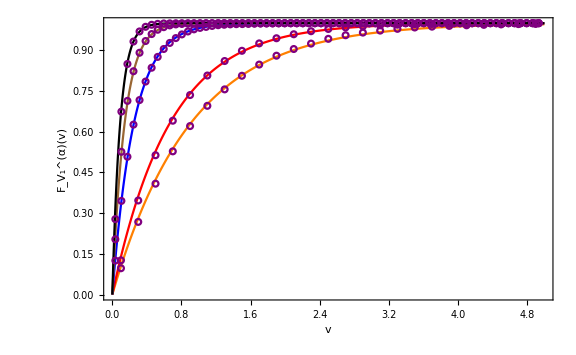

```mathematica
gStart=1; gEnd=5;
newMin=0; newMax=5;
legendCoord={0.85,0.25};

stringArray = Table[
"θ="<>ToString [thetaArray[[t]]]
(*"μ="<>ToString [muArray[[t]]]<>", θ="<>ToString [thetaArray[[t]]]<>", α="<>ToString[alphaArray[[t]]]*)
,{t,gStart,gEnd}];



gStart=Max[gStart,1]; gEnd=Min[gEnd,length];
legendPlotted=False;

oldMin=simDistArray[[All,1]]; oldMax=simDistArray[[All,2]];
newMin=Table[newMin,length];
newMax=Table[newMax,length];

plotArray=Table[
min=newMin[[t]];
max=newMax[[t]];
dx=simDistArray[[t,3]];
simDist=simDistArray[[t,4]];
hist=histArray[[t]];
color=colorArray[[t]];

thePlot=If[legendPlotted,
ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color],
ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color,PlotLegends->Placed[LineLegend[colorArray,stringArray],legendCoord]]];

simDataPoints=Table[{x+dx/2,CDF[simDist,x+dx/2]},{x,min,max-dx/2,dx}];
simPlot=If[legendPlotted,
ListPlot[simDataPoints,ImageSize->Medium,PlotRange->All,PlotMarkers->Graphics[{Purple,Thin,Circle[]},ImageSize->6]],
legendPlotted=True;ListPlot[simDataPoints,ImageSize->Medium,PlotRange->All,PlotMarkers->Graphics[{Purple,Thin,Circle[]},ImageSize->6],PlotLegends->Placed[{"Simulation"},legendCoord]]];

{thePlot,simPlot,hist,color},
{t,gStart,gEnd}];

Show[Flatten[{plotArray[[All,1]],plotArray[[All,2]]}],PlotRange->{{Min[newMin],Max[newMax]},All},PlotRangePadding->{{0},{0.0}},ImageSize->Large, Frame->True,FrameLabel->{{"F_V_1^(α)(v)",None},{"v",None}}, FrameStyle->Directive[Automatic, 15, Bold]]
(*Show[Flatten[{histArray[[All]],plotArray[[All,1]],plotArray[[All,2]]}],PlotRange->{{Min[newMin],Max[newMax]},All},ImageSize->Large]*)
```